```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

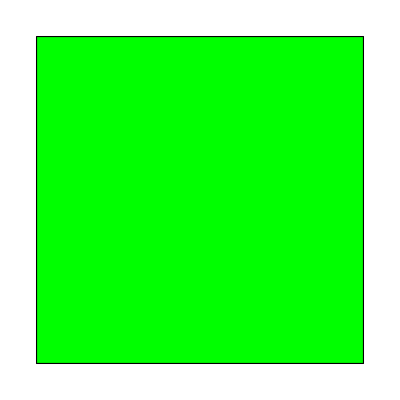

```mathematica
(*Uvozimo elemente ter node*)
Elements = Import["elements.txt","Table","FieldSeparators"->","];
Nodes = Import["nodes.txt","Table","FieldSeparators"->","];
Nodes = Drop[Nodes, None, {1}];(*odstrani prvi stolpec*)
Elements = Drop[Elements, None, {1}];

(*Prikaz elementov*)
ELplot= Table[{
	Graphics[{Green,EdgeForm[Black],Polygon[Nodes[[Elements[[i]]]]]}]},
	{i,1,Length[Elements]}];
Show[ELplot]
```

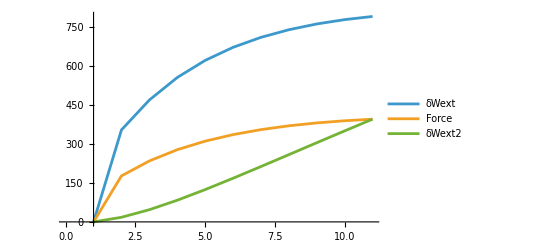

```mathematica
(*Uvoz podatkov -> Sila*)
Force = Import["sila.txt", "Table", HeaderLines -> 3][[1;;-5,2]];
T = Import["sila.txt", "Table", HeaderLines -> 3][[1;;-5,1]];
δWext = 2 * Force;
(*Pomiki ter napetosti*)
U = Import["pomik.txt", "Table", HeaderLines -> 3][[1;;-5, 2]];
Nap = Import["stress.txt", "Table", HeaderLines -> 4][[1;;-5, 2;;4]];
δWext2 = Force U;

ListLinePlot[{δWext, Force, δWext2}, AxesOrigin->{1,0}, PlotLegends->{"δWext","Force" ,"δWext2"}]
```

```mathematica
Nap // MatrixForm
```

(0. | 0. | 0.
194.265 | 3.37458×10^-15 | -0.00372638
280.809 | -1.56437×10^-15 | 0.035997
360.421 | -3.01007×10^-17 | 0.0564863
434.13 | 6.16342×10^-15 | 0.0636012
502.754 | -6.90929×10^-15 | 0.0659995
566.949 | 7.70401×10^-15 | 0.0660674
627.253 | 2.02589×10^-15 | 0.065018
684.111 | 6.82228×10^-14 | 0.0634646
737.895 | -6.96267×10^-14 | 0.061716
788.921 | 1.82939×10^-14 | 0.0599239)

```mathematica
(*Uvoz gradientov*)
(*FJSON[frame][element][Gauss Integration Point][Variable -> x,y,F]*)
(*F = FJSON[ToString[frame]][ToString[element]][ToString[integracijsaTocka]]["F"];*)
FJSON = Import["/Users/vid/Documents/FS-MAG/5. Magisterij/Projektni Praktikum/log2grad/Log2F/Grad_0_PHANTOM.json","RawJSON"];
```

```mathematica
(*Iteracija po framih*)
Frames = Length[Keys[FJSON]];
nelements = Length[Keys[FJSON[["1"]]]];
ngpoint = Length[Keys[FJSON[["1"]][[ToString[Keys[FJSON[["1"]]][[1]]]]]]];
Δt = 1/(Frames-1);

(*pred racunanjem dela izracunam Velocity gradient -> δv *)
δv = Table[{},{i,Frames}];
δv[[-1]] = {0,0,0,0,0}; (*zadnja vrstica*)
iterableFrames = 10;
For[frame=0, frame < iterableFrames, frame++,
	For[nele = 1, nele <= nelements, nele++,
	For[ngp = 1, ngp <= ngpoint, ngp++,
		Print["Frame, ",frame+1," Integracijska tocka: ",ngp];
		Subscript[F, t] = FJSON[[ToString[frame]]][[ToString[nele]]][[ToString[ngp]]][["F"]] ;
		Subscript[F, t+1]= FJSON[[ToString[frame+1]]][[ToString[nele]]][[ToString[ngp]]][["F"]];
		Print["F_t: ",Subscript[F, t]];
		Print["F_(t + 1): ",Subscript[F, t+1]];
		Print[Subscript[F, t+1] - Subscript[F, t]];
		δv[[frame+1]] = 1/Δt (Subscript[F, t+1] - Subscript[F, t]);
]; (*gp*)
]; (*element*)
];(*frame*)
```

Frame, 1 Integracijska tocka: 1

F_t: {1,0,0,1,1}

F_(t + 1): {1.1,3.92962×10^-37,5.20417×10^-18,0.953672,0.953253}

{0.1,3.92962×10^-37,5.20417×10^-18,-0.0463276,-0.0467472}

Frame, 1 Integracijska tocka: 2

F_t: {1,0,0,1,1}

F_(t + 1): {1.1,1.05294×10^-37,5.20417×10^-18,0.953672,0.953253}

{0.1,1.05294×10^-37,5.20417×10^-18,-0.0463276,-0.0467472}

Frame, 1 Integracijska tocka: 3

F_t: {1,0,0,1,1}

F_(t + 1): {1.1,3.92962×10^-37,-1.38778×10^-17,0.953672,0.953253}

{0.1,3.92962×10^-37,-1.38778×10^-17,-0.0463276,-0.0467472}

Frame, 1 Integracijska tocka: 4

F_t: {1,0,0,1,1}

F_(t + 1): {1.1,1.05294×10^-37,-1.38778×10^-17,0.953672,0.953253}

{0.1,1.05294×10^-37,-1.38778×10^-17,-0.0463276,-0.0467472}

Frame, 2 Integracijska tocka: 1

F_t: {1.1,3.92962×10^-37,5.20417×10^-18,0.953672,0.953253}

F_(t + 1): {1.2,4.87601×10^-36,3.46945×10^-18,0.913177,0.912565}

{0.1,4.48305×10^-36,-1.73472×10^-18,-0.040495,-0.0406883}

Frame, 2 Integracijska tocka: 2

F_t: {1.1,1.05294×10^-37,5.20417×10^-18,0.953672,0.953253}

F_(t + 1): {1.2,1.30652×10^-36,3.46945×10^-18,0.913177,0.912565}

{0.1,1.20123×10^-36,-1.73472×10^-18,-0.040495,-0.0406883}

Frame, 2 Integracijska tocka: 3

F_t: {1.1,3.92962×10^-37,-1.38778×10^-17,0.953672,0.953253}

F_(t + 1): {1.2,4.87601×10^-36,-1.38778×10^-17,0.913177,0.912565}

{0.1,4.48305×10^-36,0.,-0.040495,-0.0406883}

Frame, 2 Integracijska tocka: 4

F_t: {1.1,1.05294×10^-37,-1.38778×10^-17,0.953672,0.953253}

F_(t + 1): {1.2,1.30652×10^-36,-1.38778×10^-17,0.913177,0.912565}

{0.1,1.20123×10^-36,0.,-0.040495,-0.0406883}

Frame, 3 Integracijska tocka: 1

F_t: {1.2,4.87601×10^-36,3.46945×10^-18,0.913177,0.912565}

F_(t + 1): {1.3,5.30471×10^-36,6.93889×10^-18,0.877445,0.876671}

{0.1,4.28697×10^-37,3.46945×10^-18,-0.0357327,-0.035893}

Frame, 3 Integracijska tocka: 2

F_t: {1.2,1.30652×10^-36,3.46945×10^-18,0.913177,0.912565}

F_(t + 1): {1.3,1.42139×10^-36,6.93889×10^-18,0.877445,0.876671}

{0.1,1.14869×10^-37,3.46945×10^-18,-0.0357327,-0.035893}

Frame, 3 Integracijska tocka: 3

F_t: {1.2,4.87601×10^-36,-1.38778×10^-17,0.913177,0.912565}

F_(t + 1): {1.3,5.30471×10^-36,-1.38778×10^-17,0.877445,0.876671}

{0.1,4.28697×10^-37,0.,-0.0357327,-0.035893}

Frame, 3 Integracijska tocka: 4

F_t: {1.2,1.30652×10^-36,-1.38778×10^-17,0.913177,0.912565}

F_(t + 1): {1.3,1.42139×10^-36,-1.38778×10^-17,0.877445,0.876671}

{0.1,1.14869×10^-37,0.,-0.0357327,-0.035893}

Frame, 4 Integracijska tocka: 1

F_t: {1.3,5.30471×10^-36,6.93889×10^-18,0.877445,0.876671}

F_(t + 1): {1.4,5.37584×10^-36,6.93889×10^-18,0.845607,0.844702}

{0.1,7.11291×10^-38,0.,-0.0318379,-0.0319696}

Frame, 4 Integracijska tocka: 2

F_t: {1.3,1.42139×10^-36,6.93889×10^-18,0.877445,0.876671}

F_(t + 1): {1.4,1.44045×10^-36,6.93889×10^-18,0.845607,0.844702}

{0.1,1.9059×10^-38,0.,-0.0318379,-0.0319696}

Frame, 4 Integracijska tocka: 3

F_t: {1.3,5.30471×10^-36,-1.38778×10^-17,0.877445,0.876671}

F_(t + 1): {1.4,5.37584×10^-36,0.,0.845607,0.844702}

{0.1,7.11291×10^-38,1.38778×10^-17,-0.0318379,-0.0319696}

Frame, 4 Integracijska tocka: 4

F_t: {1.3,1.42139×10^-36,-1.38778×10^-17,0.877445,0.876671}

F_(t + 1): {1.4,1.44045×10^-36,0.,0.845607,0.844702}

{0.1,1.9059×10^-38,1.38778×10^-17,-0.0318379,-0.0319696}

Frame, 5 Integracijska tocka: 1

F_t: {1.4,5.37584×10^-36,6.93889×10^-18,0.845607,0.844702}

F_(t + 1): {1.5,5.29479×10^-36,6.93889×10^-18,0.817004,0.81599}

{0.1,-8.10505×10^-38,0.,-0.028603,-0.0287122}

Frame, 5 Integracijska tocka: 2

F_t: {1.4,1.44045×10^-36,6.93889×10^-18,0.845607,0.844702}

F_(t + 1): {1.5,1.41873×10^-36,6.93889×10^-18,0.817004,0.81599}

{0.1,-2.17174×10^-38,0.,-0.028603,-0.0287122}

Frame, 5 Integracijska tocka: 3

F_t: {1.4,5.37584×10^-36,0.,0.845607,0.844702}

F_(t + 1): {1.5,5.29479×10^-36,0.,0.817004,0.81599}

{0.1,-8.10505×10^-38,0.,-0.028603,-0.0287122}

Frame, 5 Integracijska tocka: 4

F_t: {1.4,1.44045×10^-36,0.,0.845607,0.844702}

F_(t + 1): {1.5,1.41873×10^-36,0.,0.817004,0.81599}

{0.1,-2.17174×10^-38,0.,-0.028603,-0.0287122}

Frame, 6 Integracijska tocka: 1

F_t: {1.5,5.29479×10^-36,6.93889×10^-18,0.817004,0.81599}

F_(t + 1): {1.6,5.12776×10^-36,1.38778×10^-17,0.791122,0.790017}

{0.1,-1.67028×10^-37,6.93889×10^-18,-0.0258814,-0.0259729}

Frame, 6 Integracijska tocka: 2

F_t: {1.5,1.41873×10^-36,6.93889×10^-18,0.817004,0.81599}

F_(t + 1): {1.6,1.37398×10^-36,1.38778×10^-17,0.791122,0.790017}

{0.1,-4.47549×10^-38,6.93889×10^-18,-0.0258814,-0.0259729}

Frame, 6 Integracijska tocka: 3

F_t: {1.5,5.29479×10^-36,0.,0.817004,0.81599}

F_(t + 1): {1.6,5.12776×10^-36,0.,0.791122,0.790017}

{0.1,-1.67028×10^-37,0.,-0.0258814,-0.0259729}

Frame, 6 Integracijska tocka: 4

F_t: {1.5,1.41873×10^-36,0.,0.817004,0.81599}

F_(t + 1): {1.6,1.37398×10^-36,0.,0.791122,0.790017}

{0.1,-4.47549×10^-38,0.,-0.0258814,-0.0259729}

Frame, 7 Integracijska tocka: 1

F_t: {1.6,5.12776×10^-36,1.38778×10^-17,0.791122,0.790017}

F_(t + 1): {1.7,4.91493×10^-36,1.38778×10^-17,0.767557,0.766374}

{0.1,-2.12828×10^-37,0.,-0.0235657,-0.0236431}

Frame, 7 Integracijska tocka: 2

F_t: {1.6,1.37398×10^-36,1.38778×10^-17,0.791122,0.790017}

F_(t + 1): {1.7,1.31695×10^-36,1.38778×10^-17,0.767557,0.766374}

{0.1,-5.70272×10^-38,0.,-0.0235657,-0.0236431}

Frame, 7 Integracijska tocka: 3

F_t: {1.6,5.12776×10^-36,0.,0.791122,0.790017}

F_(t + 1): {1.7,4.91493×10^-36,0.,0.767557,0.766374}

{0.1,-2.12828×10^-37,0.,-0.0235657,-0.0236431}

Frame, 7 Integracijska tocka: 4

F_t: {1.6,1.37398×10^-36,0.,0.791122,0.790017}

F_(t + 1): {1.7,1.31695×10^-36,0.,0.767557,0.766374}

{0.1,-5.70272×10^-38,0.,-0.0235657,-0.0236431}

Frame, 8 Integracijska tocka: 1

F_t: {1.7,4.91493×10^-36,1.38778×10^-17,0.767557,0.766374}

F_(t + 1): {1.8,4.6805×10^-36,3.46945×10^-17,0.745981,0.744732}

{0.1,-2.34435×10^-37,2.08167×10^-17,-0.0215759,-0.021642}

Frame, 8 Integracijska tocka: 2

F_t: {1.7,1.31695×10^-36,1.38778×10^-17,0.767557,0.766374}

F_(t + 1): {1.8,1.25414×10^-36,3.46945×10^-17,0.745981,0.744732}

{0.1,-6.28166×10^-38,2.08167×10^-17,-0.0215759,-0.021642}

Frame, 8 Integracijska tocka: 3

F_t: {1.7,4.91493×10^-36,0.,0.767557,0.766374}

F_(t + 1): {1.8,4.6805×10^-36,8.32667×10^-17,0.745981,0.744732}

{0.1,-2.34435×10^-37,8.32667×10^-17,-0.0215759,-0.021642}

Frame, 8 Integracijska tocka: 4

F_t: {1.7,1.31695×10^-36,0.,0.767557,0.766374}

F_(t + 1): {1.8,1.25414×10^-36,8.32667×10^-17,0.745981,0.744732}

{0.1,-6.28166×10^-38,8.32667×10^-17,-0.0215759,-0.021642}

Frame, 9 Integracijska tocka: 1

F_t: {1.8,4.6805×10^-36,3.46945×10^-17,0.745981,0.744732}

F_(t + 1): {1.9,4.43909×10^-36,6.93889×10^-18,0.726129,0.724824}

{0.1,-2.41412×10^-37,-2.77556×10^-17,-0.0198513,-0.0199081}

Frame, 9 Integracijska tocka: 2

F_t: {1.8,1.25414×10^-36,3.46945×10^-17,0.745981,0.744732}

F_(t + 1): {1.9,1.18945×10^-36,6.93889×10^-18,0.726129,0.724824}

{0.1,-6.46861×10^-38,-2.77556×10^-17,-0.0198513,-0.0199081}

Frame, 9 Integracijska tocka: 3

F_t: {1.8,4.6805×10^-36,8.32667×10^-17,0.745981,0.744732}

F_(t + 1): {1.9,4.43909×10^-36,-2.77556×10^-17,0.726129,0.724824}

{0.1,-2.41412×10^-37,-1.11022×10^-16,-0.0198513,-0.0199081}

Frame, 9 Integracijska tocka: 4

F_t: {1.8,1.25414×10^-36,8.32667×10^-17,0.745981,0.744732}

F_(t + 1): {1.9,1.18945×10^-36,-2.77556×10^-17,0.726129,0.724824}

{0.1,-6.46861×10^-38,-1.11022×10^-16,-0.0198513,-0.0199081}

Frame, 10 Integracijska tocka: 1

F_t: {1.9,4.43909×10^-36,6.93889×10^-18,0.726129,0.724824}

F_(t + 1): {2.,4.19949×10^-36,6.93889×10^-18,0.707785,0.70643}

{0.1,-2.39596×10^-37,0.,-0.0183449,-0.018394}

Frame, 10 Integracijska tocka: 2

F_t: {1.9,1.18945×10^-36,6.93889×10^-18,0.726129,0.724824}

F_(t + 1): {2.,1.12525×10^-36,6.93889×10^-18,0.707785,0.70643}

{0.1,-6.41995×10^-38,0.,-0.0183449,-0.018394}

Frame, 10 Integracijska tocka: 3

F_t: {1.9,4.43909×10^-36,-2.77556×10^-17,0.726129,0.724824}

F_(t + 1): {2.,4.19949×10^-36,0.,0.707785,0.70643}

{0.1,-2.39596×10^-37,2.77556×10^-17,-0.0183449,-0.018394}

Frame, 10 Integracijska tocka: 4

F_t: {1.9,1.18945×10^-36,-2.77556×10^-17,0.726129,0.724824}

F_(t + 1): {2.,1.12525×10^-36,0.,0.707785,0.70643}

{0.1,-6.41995×10^-38,2.77556×10^-17,-0.0183449,-0.018394}

```mathematica
δWint = {}; (*Notranje virtualno delo za vse frame*)
(*Jacobian matrix*)
(*Mapping the determinant*)


For[frame = 1, frame <= Frames, frame ++,
det = {};
Subscript[𝒯, 1] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,-1};
Subscript[𝒯, 2] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,-1};
Subscript[𝒯, 3] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,1};
Subscript[𝒯, 4] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,1};
Subscript[ψ, i_][𝒳_, 𝒴_] := 1/4(1 + Subscript[𝒯, i][[1]] * 𝒳) *(1 + Subscript[𝒯, i][[2]]  * 𝒴);


For[j =1, j <= Length[Elements], j++,
	x = Nodes[[Elements[[j]]]][[;;,1]];
	y = Nodes[[Elements[[j]]]][[;;,2]];

	X[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] x[[i]],{i,1,4}];
	Y[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] y[[i]],{i,1,4}];
	J[𝒳_, 𝒴_]  = ({{D[X[𝒳, 𝒴], 𝒳], D[Y[𝒳, 𝒴], 𝒳]}, {D[X[𝒳, 𝒴], 𝒴], D[Y[𝒳, 𝒴], 𝒴]}});
	(*J[𝒳_, 𝒴_] = ({{D[X[𝒳, 𝒴],𝒳], D[Y[𝒳, 𝒴],𝒳]}, {D[X[𝒳, 𝒴],𝒴], D[Y[𝒳, 𝒴],𝒴]}});*)
];
det = Append[det,
{
Det[J[-1/(√3),-1/(√3)]],
Det[J[1/(√3),-1/(√3)]],
Det[J[-1/(√3),1/(√3)]],
Det[J[1/(√3),1/(√3)]]
}
];

(*
1. For -> index ele -> elementi
	2. For -> index gp -> integrac. tocka
*)
Fframe = FJSON[ ToString[frame]];

For[ele=1, ele <= Length[Elements], ele++,
Fele = Fframe[ ToString[ele]];
δWinte = 0;
For[gp = 1, gp <= 4, gp++,
	(*Napetosti*)
	σ11 = Nap[[frame,1]]; (*Prvi stolpec*)
	σ12 = Nap[[frame,2]]; (*Drugi stolpec*)
	σ22 = Nap[[frame,3]] ; 
	
	(*δv -> Ḟ*)
	δvf = δv[[frame]];
	δv11 = δvf[[1]];
	δv12 = δvf[[2]];
	δv21 = δvf[[3]];
	δv22 = δvf[[4]];
	δv33 = δvf[[5]];

			
	(*1. Piola-Kirchoff Stress -> p*)
	p11 = δv33 (δv22 σ11 - δv12 σ12);
	p12 = - δv21 δv33 σ11 + δv11 δv33 σ12;
	p21 = δv33 (δv22 σ12 - δv12 σ22);
	p22 = -δv21 δv22 σ12 + δv11 δv33 σ22;
			

	(*Print[δWinti]*)
	δW = (p11 δv11 + p12 δv12 + p21 δv21 + p22 δv22) *det[[1,gp]];
	δWinte += δW; (*Sum dela vseh gaussovih tock*)
];

(*
	To ni pravilno -> Potrebujemo gradient histrosi (velocity gradient);
*)
	δWint = Append[δWint, δWinte];
]

];
```

```mathematica
δWint
```

{0.,32.0079,36.0199,36.691,35.6585,33.8003,31.5921,29.2924,27.0387,24.9013,0.}

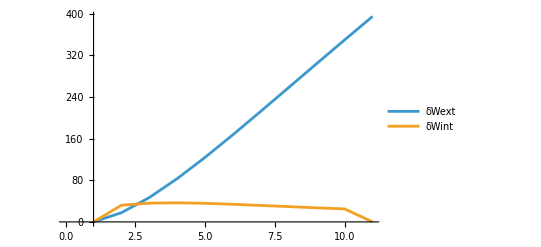

```mathematica
ListLinePlot[{δWext2, δWint},AxesOrigin->{1,0}, PlotLegends->{"δWext","δWint"}]
```

```mathematica
{Nap // MatrixForm , U// MatrixForm ,Force // MatrixForm}
```

{(0. | 0. | 0.
194.265 | 3.37458×10^-15 | -0.00372638
280.809 | -1.56437×10^-15 | 0.035997
360.421 | -3.01007×10^-17 | 0.0564863
434.13 | 6.16342×10^-15 | 0.0636012
502.754 | -6.90929×10^-15 | 0.0659995
566.949 | 7.70401×10^-15 | 0.0660674
627.253 | 2.02589×10^-15 | 0.065018
684.111 | 6.82228×10^-14 | 0.0634646
737.895 | -6.96267×10^-14 | 0.061716
788.921 | 1.82939×10^-14 | 0.0599239),(0.
0.1
0.2
0.3
0.4
0.5
0.6
0.7
0.8
0.9
1.),(0.
176.604
234.007
277.247
310.093
335.169
354.343
368.972
380.061
388.366
394.46)}

```mathematica
{Length[Force],Length[U],Length[Nap]}
```

{11,11,11}

```mathematica
Keys[FJSON]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
{δWext, δWint}
```

{{0.,353.208,468.014,554.494,620.186,670.338,708.686,737.944,760.122,776.732,788.92},{0.,32.0079,36.0199,36.691,35.6585,33.8003,31.5921,29.2924,27.0387,24.9013,0.}}